## 1/16 BPS

“Words to describe a black hole” (2209.06728).

### Load data

```mathematica
Do[
cohomology[NN]=Import[NotebookDirectory[]<>"cohomology_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
MaxLevel[NN_] := Switch[NN,
2,25,
3,19,
4,15];
NumAllStatesUpToLevel[NN_,level_] := Total[#[[9]]&/@Select[cohomology[NN],#[[1]]<=level&]];
NumAllStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,9]];
NumMultiGravitonStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,10]];
```

```mathematica
(* Usage example *)
NumAllStates[2,{0,0,4,4,4},7]
NumMultiGravitonStates[2,{0,0,4,4,4},7]
```

1

0

### U(1) partition function

```mathematica
level=25;
ZU1sw[x_,a_,b_,u_,v_,w_]:=(a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b)) x
ZU1B[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]+ZU1sw[-x,a,b,-u,-v,-w])
ZU1F[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]-ZU1sw[-x,a,b,-u,-v,-w])

ZU1[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(ZU1B[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n ZU1F[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
ZU1reduced[x_]:=ZU1[1,x^3,x^3,x^2,x^2,x^2]
IU1reduced[x_]:=ZU1[-1,x^3,x^3,-x^2,-x^2,-x^2]
```

### Partition function

```mathematica
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
PermutationMultiplicity[charges_] := Length[Permutations[charges[[1;;2]]]]*Length[Permutations[charges[[3;;5]]]];
Index[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[3;;5]]) PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
NumAllStates[NN_,charges_] := Sum[ PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
Index[NN_,level_] := Sum[Index[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
NumAllStates[NN_,level_] := Sum[NumAllStates[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
Index[NN_] := Index[NN] = Series[(1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
NumAllStates[NN_] :=NumAllStates[NN] = Series[(1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UIndex[NN_] := UIndex[NN] = Series[IU1reduced[x] (1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UNumAllStates[NN_] := UNumAllStates[NN] = Series[ZU1reduced[x] (1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

```mathematica
UIndex[2]
```

1+3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+O[x]^26

```mathematica
Index[2]
```

1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25+O[x]^26

### Tables

```mathematica
NN = 2;
StringReplace[Join[{{"Level","SU","SU Index","U", "U Index"}},Join[{Range[0,MaxLevel[NN]]},CoefficientList[{NumAllStates[NN],Index[NN],UNumAllStates[NN],UIndex[NN]},x]]//Transpose]//MatrixForm//TeXForm//ToString,{"\\\\"->"\\\\\\hline"}]
```

\left(
\begin{array}{ccccc}
 \text{Level} & \text{SU} & \text{SU Index} & \text{U} & \text{U Index} \\\hline
 0 & 1 & 1 & 1 & 1 \\\hline
 1 & 0 & 0 & 0 & 0 \\\hline
 2 & 0 & 0 & 3 & 3 \\\hline
 3 & 0 & 0 & 2 & -2 \\\hline
 4 & 6 & 6 & 15 & 9 \\\hline
 5 & 6 & -6 & 18 & -6 \\\hline
 6 & 9 & -7 & 51 & 11 \\\hline
 7 & 18 & 18 & 90 & -6 \\\hline
 8 & 30 & 6 & 195 & 9 \\\hline
 9 & 40 & -36 & 362 & 14 \\\hline
 10 & 66 & 6 & 699 & -21 \\\hline
 11 & 120 & 84 & 1308 & 36 \\\hline
 12 & 198 & -80 & 2431 & -17 \\\hline
 13 & 324 & -132 & 4434 & -18 \\\hline
 14 & 537 & 309 & 8046 & 114 \\\hline
 15 & 822 & -18 & 14346 & -194 \\\hline
 16 & 1257 & -567 & 25434 & 258 \\\hline
 17 & 1944 & 516 & 44544 & -168 \\\hline
 18 & 2959 & 613 & 77442 & -112 \\\hline
 19 & 4476 & -1392 & 133386 & 630 \\\hline
 20 & 6834 & -180 & 228021 & -1089 \\\hline
 21 & 10352 & 2884 & 386898 & 1130 \\\hline
 22 & 15540 & -1926 & 651843 & -273 \\\hline
 23 & 23406 & -4242 & 1091004 & -1632 \\\hline
 24 & 35076 & 7890 & 1814578 & 4104 \\\hline
 25 & 52020 & 792 & 2999724 & -5364 \\\hline
\end{array}
\right)

### Plots

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 1.5;
```

```mathematica
Do[
Export["/Users/yinhslin/git/bh/SU"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[NumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[Index[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["SU("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}},TicksStyle->Directive[Black,size]]];
Export["/Users/yinhslin/git/bh/U"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[UNumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[UIndex[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["U("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}}]];
,{NN,2,4}
]
```

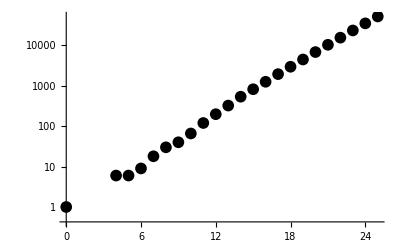

```mathematica
NN=2;
ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[NumAllStates[NN],x]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag],MaTeX["\\text{\\#states}",Magnification->mag]},PlotLabel->MaTeX["\\mathrm{SU}("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}},TicksStyle->Directive[Black,size]]
```

## Near-BPS anomalous dimensions

“Decoding stringy near-supersymmetric black holes” (2306.04673).

### Load anomalous dimensions from CSV

Can skip if “ad.mx” exists.

```mathematica
(*
Do[
ad[NN]=Import[NotebookDirectory[]<>"ad_"<>ToString[NN]<>".csv"];
,
{NN,{0,2,3,4}}
];
ad[0]=Table[Insert[r,0,8],{r,ad[0]}];
DumpSave[NotebookDirectory[]<>"ad.mx",ad];
*)
```

### Load anomalous dimensions from MX

```mathematica
Import[NotebookDirectory[]<>"ad.mx"];
```

```mathematica
MaxLevel[NN_] := Switch[NN,
-1,22,(*planar plethystic*)
0,22,(*planar*)
2,24,
3,17,
4,15];
OrganizeData[data_]:=Tally[Sort[Flatten[#[[9;;]]&/@data]]];
AD[NN_]:=ad[NN]//OrganizeData;
AD[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]//OrganizeData];
AD[NN_,charges_,degree_]:=AD[NN,charges,degree]=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&&#[[7]]==degree&]//OrganizeData];
ADUpToLevel[NN_,level_]:=Select[ad[NN],#[[1]]<=level&]//OrganizeData;
Charges[level_]:=Flatten[#]&/@DeleteDuplicates[{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers]];
chargeConversion=({{-1/2, 0, 1/2, 1/2, 1/2, 1}, {1/2, 1/2, 0, 0, 0, 0}, {1/2, -1/2, 0, 0, 0, 0}, {1/2, 0, 1/2, -1/2, -1/2, 0}, {1/2, 0, -1/2, 1/2, -1/2, 0}, {1/2, 0, -1/2, -1/2, 1/2, 0}});
```

### Multi-particle from single-particle for SU(∞)

Can skip if “ad_-1.mx” exists.

```mathematica
ZAtLevel[NN_,l_]:=ZAtLevel[NN,l]=Module[{d},Sum[ a^c[[1]] b^c[[2]] u^c[[3]] v^c[[4]] w^c[[5]] x^d t1^ed[[1]] ed[[2]],{c,Charges[l]},{d,2,Total[c]},{ed,AD[NN,c,d]}]]
Z[NN_,L_]:=Z[NN,L]=Sum[ZAtLevel[NN,l],{l,4,L}]
ZB[L_,ap_,bp_,up_,vp_,wp_,xp_,t1p_]:=1/2(Z[0,L]+(Z[0,L]/.{u->-u,v->-v,w->-w,x->-x}))/.{a->ap,b->bp,u->up,v->vp,w->wp,x->xp,t1->t1p}
ZF[L_,ap_,bp_,up_,vp_,wp_,xp_,t1p_]:=1/2(Z[0,L]-(Z[0,L]/.{u->-u,v->-v,w->-w,x->-x}))/.{a->ap,b->bp,u->up,v->vp,w->wp,x->xp,t1->t1p}
```

```mathematica
(*L=22;
Zexp[L]=1/n(ZB[L,(t^3 a)^n,(t^3 b)^n,(t^2 u)^n,(t^2 v)^n,(t^2 w)^n,x^n,t1^n]+(-1)^(n+1)ZF[L,(t^3 a)^n,(t^3 b)^n,(t^2 u)^n,(t^2 v)^n,(t^2 w)^n,x^n,t1^n]);
Zmulti[L]=Exp[Sum[Zexp[L]/. (t1^n_)^a_:>t1^(n*a),{n,1,Ceiling[L/4]}]];
Zmulti[L]=Series[Zmulti[L],{t,0,L}]//Normal//Expand;
monomialToList[m_]:=Module[{exp,multi}, exp=Exponent[m,{t,a,b,u,v,w,x,t1}];
exp=Join[exp[[1;;7]]//Round,{exp[[8]]}];
multi=Coefficient[m,t^(exp[[1]]//Round)a^(exp[[2]]//Round)b^(exp[[3]]//Round)u^(exp[[4]]//Round)v^(exp[[5]]//Round)w^(exp[[6]]//Round)x^(exp[[7]]//Round)t1^exp[[8]]];
exp=Join[exp[[1;;7]],{-1},Table[exp[[8]],{multi}]]
];
adMulti[L]=monomialToList/@DeleteCases[List@@Zmulti[L],1]//Sort;
ad[-1]=Module[{grouped,processGroup},
grouped=GroupBy[adMulti[L],#[[1;;8]]&];
processGroup[key_,group_]:=Join[key,Flatten[group[[All,9;;]]]];
KeyValueMap[processGroup,grouped]/.{1.->1,2.->2,3.->3}
];
Export[NotebookDirectory[]<>"ad_-1.mx",ad[-1]];*)
```

### Decompose into primaries and multiplets of centralizer C(Δ)

Can skip if “primaries.m” and “multiplets.m” exist.

#### Primary characters

```mathematica
χsu2[m_][t_]:=(t^(1/2(2m+1))-t^(-1/2(2m+1)))/(t^(1/2)-t^(-1/2));
χsu3[m1_,m2_][t1_,t2_]:=t1^(m1+2m2)Sum[t1^(-3/2(k+l))(t1^((k-l+1)/2)t2^(-(k-l+1))-t1^(-(k-l+1)/2)t2^((k-l+1)))/(t1^(1/2)t2^-1-t1^(-1/2)t2),{k,m2,m1+m2},{l,0,m2}];
χ[EE_,JL_,JR_,q1_,q2_,q3_]:=Module[{s3,t2},Exp[-β EE-JL(ω1+ω2)-1/3(Δ1+Δ2+Δ3)(q1+q2+q3)]χsu2[JR][Exp[-(ω1-ω2)]]/(1-Exp[-β-ω1])/(1-Exp[-β-ω2])χsu3[q1-q2,q2-q3][Exp[-1/3(2Δ1-Δ2-Δ3)],Exp[-1/3(Δ1+Δ2-2Δ3)]](1+Exp[-1/2(β-ω1-ω2+ Δ1+ Δ2+ Δ3)])(1+Exp[-1/2(β+ω1+ω2- Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1+ω2- Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β+ω1+ω2+ Δ1- Δ2- Δ3)])
(1+Exp[-1/2(β+ω1-ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β-ω1+ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1+ Δ2- Δ3)])
];
χPrimary[JL_,JR_,q1_,q2_,q3_]:=Module[{s3,t2},Exp[-JL(ω1+ω2)-1/3(Δ1+Δ2+Δ3)(q1+q2+q3)]χsu2[JR][Exp[-(ω1-ω2)]]χsu3[q1-q2,q2-q3][Exp[-1/3(2Δ1-Δ2-Δ3)],Exp[-1/3(Δ1+Δ2-2Δ3)]]
];
fugacity={β->-2Log[t0],ω1->-2Log[a]-Log[t0],ω2->-2Log[b]-Log[t0],Δ1->-2Log[u],Δ2->-2Log[v],Δ3->-2Log[w]};
```

#### Multiplets

```mathematica
ZAtLevel[NN_,l_,Δ_]:=ZAtLevel[NN,l,Δ]=Module[{d},Sum[(a b)^(Total[c]-d)(a/ b)^(c[[1]]-c[[2]])u^(c[[3]]-c[[4]]-c[[5]]+d)v^(-c[[3]]+c[[4]]-c[[5]]+d)w^(-c[[3]]-c[[4]]+c[[5]]+d)t0^l ed[[2]],{c,Charges[l]},{d,2,Total[c]},{ed,Select[AD[NN,c,d],#[[1]]==Δ&]}]];
Z[NN_,L_,Δ_]:=Z[NN,L,Δ]=Sum[ZAtLevel[NN,l,Δ],{l,4,L}]
```

```mathematica
FindLeadingTerm[f_,t0_]:=Module[{order=0,series,normal,terms,leadingTerm=0},
While[leadingTerm==0,series=Series[f,{t0,0,order}];normal=Normal[series];terms=MonomialList[normal,t0];If[Length[terms]>0,leadingTerm=First[terms]];order=order+1;];
leadingTerm];
HWCharge[expr_,L_]:=Module[{series,sortFunction,exp,R4,R1,R2,m,n},
(*series=Series[expr,{t0,0,L}]//Simplify;*)
series=FindLeadingTerm[expr,t0]//Simplify;
sortFunction=(#1[[1]]<#2[[1]]||(#1[[1]]==#2[[1]]&&#1[[2]]+#1[[3]]>#2[[2]]+#2[[3]])||(#1[[1]]==#2[[1]]&&#1[[2]]+#1[[3]]==#2[[2]]+#2[[3]]&&#1[[2]]-#1[[3]]>#2[[2]]-#2[[3]])||(#1[[1]]==#2[[1]]&&#1[[2]]+#1[[3]]==#2[[2]]+#2[[3]]&&#1[[2]]-#1[[3]]==#2[[2]]-#2[[3]]&&#1[[4]]-#1[[5]]>#2[[4]]-#2[[5]])||(#1[[1]]==#2[[1]]&&#1[[2]]+#1[[3]]==#2[[2]]+#2[[3]]&&#1[[2]]-#1[[3]]==#2[[2]]-#2[[3]]&&#1[[4]]-#1[[5]]==#2[[4]]-#2[[5]]&&#1[[5]]-#1[[6]]>#2[[5]]-#2[[6]])||(#1[[1]]==#2[[1]]&&#1[[2]]+#1[[3]]==#2[[2]]+#2[[3]]&&#1[[2]]-#1[[3]]==#2[[2]]-#2[[3]]&&#1[[5]]-#1[[6]]==#2[[5]]-#2[[6]]&&#1[[5]]-#1[[6]]==#2[[5]]-#2[[6]]&&#1[[4]]+#1[[5]]+#1[[6]]>#2[[4]]+#2[[5]]+#2[[6]]))&;
exp=Sort[(Exponent[#,{t0,a,b,u,v,w}]&)/@(List@@(series//Normal//Expand)),sortFunction][[1]];
R4=exp[[4]]/2+exp[[5]]/2+exp[[6]]/2;
R1=exp[[4]]/2-exp[[5]]/2;
R2=exp[[5]]/2-exp[[6]]/2;
m=R1+R2;
n=-R2;

{1/2(exp[[1]]-(exp[[2]]+exp[[3]])/2),(exp[[2]]+exp[[3]])/4,(exp[[2]]-exp[[3]])/4,1/3 (2 m+n+R4),1/3 (-m+n+R4),1/3 (-m-2 n+R4)}
];
HWCharge[expr_]:=HWCharge[expr,24];
FindMultiplets[expr_,L_]:=Module[{p={},exponent,Zexpand},
Zexpand=Series[expr,{t0,0,L}];
While[
(*((Zexpand//Normal)/.{t0->1,a->1,b->1,u->1,v->1,w->1})!=0,*)
!PossibleZeroQ[Zexpand//Normal],
exponent=HWCharge[Zexpand,L];
AppendTo[p,exponent];
Zexpand=Zexpand-Assuming[a>0&&b>0,Series[χ@@exponent/.fugacity//Simplify,{t0,0,L}]];
];
p
];
FindMultiplets[expr_]:=FindMultiplets[expr,24];
```

#### Run and save primaries

```mathematica
(*
getPowers[poly_]:=Module[{minPowers,transformedPoly,coefficients,positions,powers,powersList},minPowers=Exponent[poly,{a,b,u,v,w},Min];
transformedPoly=poly*a^(-minPowers[[1]])*b^(-minPowers[[2]])*u^(-minPowers[[3]])*v^(-minPowers[[4]])*w^(-minPowers[[5]]);
coefficients=CoefficientList[transformedPoly,{a,b,u,v,w}];
positions=Position[coefficients,_?(#!=0&)];
powers=positions+Table[minPowers,Length[positions]]-1;
powersList=Flatten[MapThread[ConstantArray,{powers,coefficients[[Sequence@@#]]&/@positions}],1];
Return[powersList];];
Do[
allPrimaries[NN]=Flatten[Table[
{ev[[1]],{(#[[1]]+#[[2]])/4,(#[[1]]-#[[2]])/4,(#[[3]])/2,(#[[4]])/2,(#[[5]])/2}&/@getPowers[Assuming[a>0&&b>0,χPrimary@@hw[[2;;]]/.fugacity/.t0->1//Together//Simplify//Expand]]}
,{ev,allMultiplets[NN]},{hw,ev[[2]]}],1];
,
{NN,{-1,0,2,3,4}}
];
Save[NotebookDirectory[]<>"primaries.m",allPrimaries];
*)
```

#### Run and save multiplets

```mathematica
(*
Do[
L=MaxLevel[NN];
Do[
AD[NN,c,d];
,{l,4,L},{c,Charges[l]},{d,2,Total[c]}
];
allMultiplets[NN]={};
i=0;
Monitor[
Do[
i=i+1;
AppendTo[allMultiplets[NN],{d,FindMultiplets[Z[NN,L,d],L]}],
{d,DeleteCases[ADUpToLevel[NN,L][[;;,1]],0]}
]
,
ToString[i]<>"/"<>ToString[Length[DeleteCases[ADUpToLevel[NN,L][[;;,1]],0]]]<>": "<>ToString[d]
]
,
{NN,{-1,0,2,3,4}}
];
Save[NotebookDirectory[]<>"multiplets.m",allMultiplets];
*)
```

### Load primaries and multiplets

```mathematica
Get[NotebookDirectory[]<>"primaries.m"];
Get[NotebookDirectory[]<>"multiplets.m"];
```

```mathematica
NN=-1;
allMultiplets[NN]//Length
Total[Length[#[[2]]]&/@allMultiplets[NN]]
```

4385

27617

## 1/8 BPS Schur gravitons

“On 1/8-BPS black holes and the chiral algebra of N=4 SYM”.
Data of direct construction of Schur graviton cohomology.

### Load data

```mathematica
Do[
cohomology[NN]=Import[NotebookDirectory[]<>"schur_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
MaxLevel[NN_] := Switch[NN,
2,24,
3,20,
4,16];
NumAllStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,9]];
PermutationMultiplicity[charges_] := Length[Permutations[charges[[4;;5]]]];
NumAllStates[NN_,charges_] := Sum[ PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
ChargeListH[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{0,nz},{0,nθ1,nθ2}}/.Solve[2 nz+nθ1+nθ2==level,{nz,nθ1,nθ2},NonNegativeIntegers],{2}]];
```

### Indices

#### Unflavored Schur

```mathematica
Clear[Schur];
Index[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[4;;5]]) PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
Schur[NN_,level_] := Sum[Index[NN,charges],{charges,ChargeListH[level]}]/;IntegerQ[level];
NumAllStates[NN_,level_] := Sum[NumAllStates[NN,charges],{charges,ChargeListH[level]}]/;IntegerQ[level];
Schur[NN_] := Schur[NN] = Series[(1+Sum[Schur[NN,level]x^level,{level,2,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
NumAllStates[NN_] :=NumAllStates[NN] = Series[(1+ Sum[NumAllStates[NN,level]x^level,{level,2,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

#### Flavored Schur

```mathematica
Clear[FlavoredSchur];
IndexNoPerm[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[4;;5]]) NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
FlavoredSchur[NN_,level_]:=Module[{Q},Sum[Q=charges[[4]]-charges[[5]];IndexNoPerm[NN,charges]If[Q==0,1,b^Q+b^-Q],{charges,ChargeListH[level]}]]/;IntegerQ[level];
FlavoredSchur[NN_]:=FlavoredSchur[NN]=Series[(1+Sum[FlavoredSchur[NN,level]x^level,{level,1,MaxLevel[NN]}]),{q,0,MaxLevel[NN]}];
```

#### Flavored MacDonald

```mathematica
Clear[FlavoredMacDonald];
IndexNoPerm[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[4;;5]]) NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
FlavoredMacDonald[NN_,level_]:=Module[{Q},Sum[Q=charges[[4]]-charges[[5]];IndexNoPerm[NN,charges] s^(charges[[4]]+charges[[5]])If[Q==0,1,b^Q+b^-Q],{charges,ChargeListH[level]}]]/;IntegerQ[level];
FlavoredMacDonald[NN_]:=FlavoredMacDonald[NN]=Series[(1+Sum[FlavoredMacDonald[NN,level] x^level,{level,1,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

## Index

### Plot setup

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->20};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 2;
```

```mathematica
Ratio[type_,NN_]:=CoefficientList[indexX[type,NN],x][[;;31]](*/CoefficientList[indexX["us",NN],x][[;;31]];*);
```

### SU(N)

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"ind.mx"];
```

```mathematica
Table[CoefficientList[indexX["fm",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["fm",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 0 | 3 | 4 | 9 | 12 | 22 | 36 | 60 | 88 | 135 | 204 | 302 | 432 | 627 | 900 | 1269 | 1764 | 2451 | 3384 | 4629 | 6268 | 8460 | 11376 | 15183 | 20124 | 26595 | 35008 | 45828 | 59700 | 77522
1 | 0 | 3 | 4 | 9 | 10 | 22 | 26 | 51 | 66 | 108 | 148 | 241 | 326 | 489 | 676 | 990 | 1358 | 1919 | 2614 | 3660 | 4958 | 6759 | 9080 | 12288 | 16354 | 21789 | 28770 | 38043 | 49842 | 65161
1 | 0 | 3 | 4 | 9 | 16 | 26 | 40 | 59 | 96 | 120 | 208 | 245 | 404 | 469 | 780 | 901 | 1436 | 1664 | 2600 | 3067 | 4620 | 5529 | 8124 | 9857 | 14040 | 17245 | 24152 | 29918 | 40920 | 51052
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 71 | 118 | 152 | 266 | 303 | 554 | 593 | 1068 | 1112 | 1974 | 2025 | 3496 | 3466 | 6034 | 5803 | 10162 | 9762 | 16840 | 16243 | 27478 | 27027 | 44432 | 44471
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 71 | 128 | 170 | 296 | 381 | 640 | 793 | 1308 | 1558 | 2504 | 2953 | 4608 | 5376 | 8132 | 9359 | 13956 | 15647 | 23276 | 25850 | 38012 | 41916 | 60848 | 66707)

(1 | 0 | 3 | 4 | 4 | 8 | 11 | 16 | 26 | 32 | 44 | 68 | 100 | 128 | 187 | 252 | 353 | 468 | 642 | 844 | 1124 | 1480 | 1936 | 2528 | 3298 | 4244 | 5460 | 7004 | 8928 | 11436 | 14475
1 | 0 | 3 | 4 | 9 | 16 | 19 | 36 | 46 | 64 | 85 | 116 | 159 | 180 | 257 | 308 | 417 | 488 | 669 | 796 | 1055 | 1276 | 1642 | 2012 | 2530 | 3132 | 3899 | 4844 | 5980 | 7356 | 9217
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 62 | 112 | 133 | 220 | 284 | 400 | 533 | 688 | 923 | 1124 | 1509 | 1792 | 2411 | 2800 | 3638 | 4392 | 5454 | 6668 | 8070 | 9796 | 11749 | 14248 | 16840
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 71 | 128 | 159 | 288 | 356 | 580 | 760 | 1104 | 1462 | 1984 | 2602 | 3400 | 4506 | 5648 | 7417 | 9136 | 11932 | 14544 | 18512 | 22640 | 28036 | 34708 | 41532)

```mathematica
Do[
data=Table[Log[#]&/@Ratio[type,NN],{type,{"fs","fm","sx"}}];
plot=ListPlot[data,PlotRange->{{0,30.5},Automatic},
AxesLabel->{MaTeX["2h",Magnification->mag],MaTeX["\\log(|d|)",Magnification->mag]},PlotLabel->MaTeX["\\mathrm{SU}("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"○",size},{"●",size},{"△",size}}];
(*Export["/Users/yinhslin/git/schur/index/SU"<>ToString[NN]<>".pdf",plot];*)
Print[plot];
,
{NN,2,10,1}
]
```

### U(N)

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"indU.mx"];
```

```mathematica
Table[CoefficientList[indexX["sx",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["sx",NN],x],{NN,1,10,2}]//MatrixForm
```

(1 | 4 | 12 | 16 | 32 | 60 | 60 | 198 | 159 | 562 | 560 | 1516 | 1806 | 4058 | 5344 | 10400 | 14246 | 26140 | 35620 | 61324 | 83886 | 142988 | 193658 | 321342 | 426389 | 689606 | 904270 | 1427764 | 1855468 | 2856610 | 3796488
1 | 4 | 12 | 32 | 74 | 124 | 138 | 342 | 768 | 880 | 1890 | 6158 | 7660 | 14204 | 50992 | 44498 | 159862 | 413558 | 338290 | 1721610 | 2350266 | 4849646 | 13872340 | 12688744 | 53834822 | 58933124 | 166982106 | 343912602 | 473866904 | 1423280906 | 1469874534
1 | 4 | 12 | 32 | 74 | 160 | 328 | 576 | 808 | 790 | 2154 | 4822 | 7442 | 7468 | 29228 | 83660 | 127949 | 125616 | 655838 | 1580460 | 1168024 | 5081746 | 16633006 | 18997112 | 42403600 | 165915986 | 213877482 | 408720154 | 1638235098 | 1974306336 | 4446326578
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1204 | 2096 | 3244 | 4160 | 4064 | 9880 | 22690 | 39284 | 41656 | 82864 | 298962 | 760594 | 1265846 | 1001766 | 4143428 | 14515994 | 27911324 | 18497702 | 90210148 | 323928224 | 570889824 | 385959414 | 2545711954
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1204 | 2196 | 3896 | 6608 | 10492 | 15072 | 18208 | 17420 | 40416 | 89920 | 162684 | 219512 | 214516 | 736832 | 2306442 | 5380530 | 9207839 | 8710648 | 18953774 | 79177146 | 208341790 | 347304474 | 218047278)

(1 | 4 | 5 | 10 | 8 | 16 | 19 | 28 | 30 | 40 | 48 | 74 | 71 | 102 | 120 | 164 | 172 | 238 | 264 | 360 | 383 | 496 | 554 | 724 | 782 | 1004 | 1108 | 1406 | 1522 | 1910 | 2103
1 | 4 | 12 | 32 | 49 | 68 | 182 | 272 | 376 | 1302 | 1262 | 3560 | 8264 | 8580 | 33658 | 27994 | 109264 | 150534 | 319364 | 657556 | 905738 | 2346776 | 2661978 | 7476892 | 8385176 | 22256720 | 26548816 | 64068806 | 82244495 | 178589316 | 243268390
1 | 4 | 12 | 32 | 74 | 160 | 279 | 348 | 512 | 1422 | 2580 | 2336 | 7912 | 24108 | 34315 | 45580 | 207130 | 357318 | 381062 | 1963568 | 3326326 | 4146136 | 19177784 | 25432026 | 51064577 | 177601690 | 137859738 | 618551086 | 1387432402 | 1450249632 | 6391596388
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1123 | 1680 | 1904 | 2804 | 7416 | 14550 | 18846 | 25146 | 97020 | 262156 | 422304 | 345382 | 1754580 | 5236738 | 7473256 | 8569134 | 46729350 | 108080488 | 74567640 | 359926318 | 1192737174 | 1496000392 | 2732616644
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1204 | 2196 | 3775 | 5948 | 8192 | 8720 | 12810 | 31358 | 63280 | 96812 | 85170 | 254780 | 853472 | 2073948 | 3518777 | 2958714 | 9088592 | 35487428 | 82083438 | 102998144 | 127210272 | 689496824 | 1831629760)

```mathematica
Do[
data=Table[Log[#]&/@Ratio[type,NN],{type,{"fs","fm","sx"}}];
plot=ListPlot[data,PlotRange->{{0,30.5},Automatic},
AxesLabel->{MaTeX["2h",Magnification->mag],MaTeX["\\log(|d|)",Magnification->mag]},PlotLabel->MaTeX["\\mathrm{U}("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"○",size},{"●",size},{"△",size}}];
(*Export["/Users/yinhslin/git/schur/index/U"<>ToString[NN]<>".pdf",plot];*)
Print[plot];
,
{NN,1,10,1}
]
```